## Importing the Imagenette Dataset

```mathematica
trainDirectory = "/home/mk/imagenette2-160/train/";
testDirectory  = "/home/mk/imagenette2-160/val/";
form = "*.JPEG";

ImportLabeldFilePaths[parentDirectory_,form_]:= Module[{paths,ExtractLabelFromFilePath,LabeledFilePath},
paths = FileNames[form,parentDirectory,2];
ExtractLabelFromFilePath[path_] := Part[FileNameSplit[path],-2];
LabeledFilePath[path_] := File[path]->ExtractLabelFromFilePath[path] ;
Return[Map[LabeledFilePath,paths]]
]
```

```mathematica
trainingDataFiles = ImportLabeldFilePaths[trainDirectory,form];
testDataFiles = ImportLabeldFilePaths[testDirectory,form];
labels = Union[trainingDataFiles[[All,2]]];
labels
```

{n01440764,n02102040,n02979186,n03000684,n03028079,n03394916,n03417042,n03425413,n03445777,n03888257}

```mathematica
Length[trainingDataFiles]
```

9469

```mathematica
Length[testDataFiles]
```

3925

```mathematica
genTrain=Function[RandomSample[trainingDataFiles,#BatchSize]]
```

RandomSample[trainingDataFiles,#BatchSize]&

```mathematica
(Import[#[[1]]]->#[[2]])& /@ genTrain[<|"BatchSize"->4|>]
```

{-Graphics-→n02102040,-Graphics-→n01440764,-Graphics-→n01440764,-Graphics-→n02979186}

## AlexNet

```mathematica
imageEncoder = NetEncoder[{"Image",{227,227},ColorSpace->"RGB"}]
```

NetEncoder[<>]

```mathematica
featureExtractor = NetChain[
{ConvolutionLayer[96,11,"Stride"->4],Ramp,PoolingLayer[3,"Stride"->2],BatchNormalizationLayer[],

ConvolutionLayer[265,5,"Stride"->1,"PaddingSize"->"Same"],Ramp,PoolingLayer[3,"Stride"->2],BatchNormalizationLayer[],


ConvolutionLayer[384,3,"Stride"->1,"PaddingSize"->"Same"],Ramp,BatchNormalizationLayer[],
ConvolutionLayer[384,3,"Stride"->1,"PaddingSize"->"Same"],Ramp,BatchNormalizationLayer[],

ConvolutionLayer[265,3,"Stride"->1,"PaddingSize"->"Same"],Ramp,BatchNormalizationLayer[],PoolingLayer[3,"Stride"->2],

FlattenLayer[]
}]
```

NetChain[<>]

```mathematica
classifier = NetChain[{
LinearLayer[4096],Ramp, DropoutLayer[0.5],
LinearLayer[4096],Ramp, DropoutLayer[0.5],
LinearLayer[10],SoftmaxLayer[]
}]
```

NetChain[<>]

```mathematica
alexNet = NetInitialize@NetChain[<|"featureExtractor"->featureExtractor,"classifier"->classifier|>,"Input"->imageEncoder]
```

NetChain[<>]

```mathematica
alexNet[-Graphics-]//Timing
```

{0.373655,{0.0433669,0.0521674,0.0598265,0.198112,0.0438733,0.279867,0.0189938,0.202548,0.0609642,0.0402808}}

```mathematica
Information[alexNet]
```

Net Information

## mini AlexNet

scale number of conv kernels by 5 and linear layer outputs also by 5

```mathematica
imageEncoder = NetEncoder[{"Image",{120,120},ColorSpace->"RGB"}]
```

NetEncoder[<>]

```mathematica
featureExtractorMini = NetChain[
{ConvolutionLayer[19,11,"Stride"->4],Ramp,PoolingLayer[3,"Stride"->2],BatchNormalizationLayer[],

ConvolutionLayer[53,5,"Stride"->1,"PaddingSize"->"Same"],Ramp,PoolingLayer[3,"Stride"->2],BatchNormalizationLayer[],


ConvolutionLayer[76,3,"Stride"->1,"PaddingSize"->"Same"],Ramp,BatchNormalizationLayer[],
ConvolutionLayer[76,3,"Stride"->1,"PaddingSize"->"Same"],Ramp,BatchNormalizationLayer[],

ConvolutionLayer[53,3,"Stride"->1,"PaddingSize"->"Same"],Ramp,BatchNormalizationLayer[],PoolingLayer[3,"Stride"->2],

FlattenLayer[]
}]
```

NetChain[<>]

```mathematica
4096/5 //N
```

819.2

```mathematica
classifierMini = NetChain[{
LinearLayer[819],Ramp, DropoutLayer[0.5],
LinearLayer[819],Ramp, DropoutLayer[0.5],
LinearLayer[10],SoftmaxLayer[]
}]
```

NetChain[<>]

```mathematica
alexNetMini = NetInitialize@NetChain[<|"featureExtractor"->featureExtractorMini,"classifier"->classifierMini|>,"Input"->imageEncoder,"Output"->NetDecoder[{"Class",labels}]]
```

NetChain[<>]

```mathematica
alexNetMini[-Graphics-]//Timing
```

{0.357928,n03888257}

```mathematica
Information[alexNetMini]
```

Net Information

```mathematica
alexNetMini = NetTrain[alexNetMini,{genTrain,"RoundLength"->Length[trainingDataFiles]},BatchSize->16,MaxTrainingRounds->50,ValidationSet->Scaled[0.1]]
```

NetChain[<>]

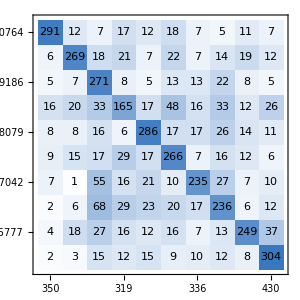
{0.655287,0.21121,actual class | -Graphics-
 | predicted class}

```mathematica
NetMeasurements[alexNetMini,testDataFiles,{"Accuracy","ErrorRate"->2,"ConfusionMatrixPlot"}]
```